```mathematica
(**Print[Parallel`Developer`KernelStatus[]];**)
nbDir=NotebookDirectory[];SetDirectory[nbDir];
Needs["GenChaosGame`"];Needs["GenDistanceFunctions`"];Needs["GenMDSTools`"];
DistributeDefinitions[nbDir];ParallelEvaluate[SetDirectory[nbDir]];
ParallelNeeds["GenChaosGame`"];ParallelNeeds["GenDistanceFunctions`"];ParallelNeeds["GenMDSTools`"];
SetSharedFunction[ParallelPrintTemporary];ParallelPrintTemporary[x_]:=PrintTemporary[x];
Print["PID:= ",$ProcessID];
Print["Before Launch:= ",ParallelEvaluate[$ProcessID]];
Needs["SubKernels`LocalKernels`"];
Block[{$mathkernel=$mathkernel<>" -threadpriority=2"},LaunchKernels[]];Print["Afte Launch:= ",ParallelEvaluate[$ProcessID]];
```

PID:= 4760

Before Launch:= {}

Afte Launch:= {6128,3652,4468,4620}

```mathematica
(** SETTINGS **)
k=9;
fragmentLength=150000;
step=fragmentLength;
dataDir="six_kingdoms";
distTag="AID";
cgrOrder={"A","C","G","T"};
ps=PointSize[0.009];
SetDirectory[FileNameJoin [{nbDir,"alltogether",dataDir,"fasta"}]];files=FileNames["*.fasta"];
SetDirectory[FileNameJoin [{nbDir,"alltogether",dataDir}]];Export["filenames.txt",StringJoin[Table[files[[i]]<>"\n",{i,1,Length@files}]]];
DistributeDefinitions[k,distTag,dataDir,cgrOrder,ps,files];
(***** end SETTINGS *****)
```

### Compute CGRs

```mathematica
splitBy=100;(* change if you want. storing fcgrs in sets of "splitBy" *)
SetDirectory[FileNameJoin[{nbDir,"alltogether",dataDir}]]; If[!DirectoryQ["fcgrs"],CreateDirectory["fcgrs"]];
SetDirectory[FileNameJoin[{nbDir,"alltogether",dataDir,"fasta"}]];
PrintTemporary[Dynamic[{i,bg,howmany,fragmentsOfThis}]];
Print[AbsoluteTiming[Monitor[allCGRs = {};howmany=0;flnames = FileNames["*.fasta"];fragmentsInEachOrganism={};
For[i = 1, i ≤ Length[flnames], i++, 
	SetDirectory[FileNameJoin[{nbDir,"alltogether",dataDir,"fasta"}]];	
	fragmentsOfThis=0;
	genome=ToUpperCase[Import[flnames[[i]]][[1]]];
	splitedgenome=StringCases[genome,cgrOrder];
	size=Length[splitedgenome];
	Print[i,") ",flnames[[i]],"  Nucleotides= ",{StringLength[genome],size},
	"  Excluded= ",StringLength[genome]-size,"  Tail= ",Mod[size,fragmentLength],
	"  Fragments= ",IntegerPart[size/fragmentLength]];
	bg=1;
	While[bg+fragmentLength<size,
		window=Take[splitedgenome,{bg,Min[bg+fragmentLength-1,size]}];
		
		(* SPARSE implementation *)
		(*nextNewCGR = sparseFCGR[StringJoin[window], cgrOrder, k][[2]];
		newCGRList=Table[nextNewCGR[[i1,1]]->nextNewCGR[[i1,2]],{i1,1,Length@nextNewCGR}];
        nextNewCGR=SparseArray[newCGRList,{2^k,2^k}];*)
		
		(* NORMAL implementation *)
		nextNewCGR = FCGR[StringJoin[window], cgrOrder, k][[2]];	

		AppendTo[allCGRs, nextNewCGR]; bg=bg+step; howmany++; fragmentsOfThis++;
		If[Mod[howmany,splitBy]==0,
			SetDirectory[FileNameJoin[{nbDir,"alltogether",dataDir,"fcgrs"}]];
			Put[Compress[allCGRs],"fcgrs_k="<>ToString[k]<>"_"<>ToString[howmany-(splitBy-1)]<>"_"<>ToString[howmany]];
			SetDirectory[FileNameJoin[{nbDir,"alltogether",dataDir,"fasta"}]]; allCGRs={};
		];
	]; AppendTo[fragmentsInEachOrganism,fragmentsOfThis];
];
If[Mod[howmany,splitBy]≠0,SetDirectory[FileNameJoin[{nbDir,"alltogether",dataDir,"fcgrs"}]]; Put[Compress[allCGRs],
"fcgrs_k="<>ToString[k]<>"_"<>ToString[IntegerPart[howmany/splitBy]*splitBy+1]<>"_"<>ToString[(IntegerPart[howmany/splitBy]+1)*splitBy]]];
, 
TableForm[{StringJoin["Reading file: ", ToString[{i,Length[flnames]}], " - ", flnames[[i]]], 
ProgressIndicator[Dynamic[i], {1, Length[flnames]}]}]];
"reading "<>ToString[i-1]<>" files"]]; Print[fragmentsInEachOrganism];
```

1) NC_000021.fasta  Nucleotides= {48129895,35106642}  Excluded= 13023253  Tail= 6642  Fragments= 234

2) NC_000913.fasta  Nucleotides= {4641652,4641652}  Excluded= 0  Tail= 141652  Fragments= 30

3) NC_001136.fasta  Nucleotides= {1531933,1531933}  Excluded= 0  Tail= 31933  Fragments= 10

4) NC_003070.fasta  Nucleotides= {30427671,30263312}  Excluded= 164359  Tail= 113312  Fragments= 201

5) NC_004317.fasta  Nucleotides= {3291871,3291834}  Excluded= 37  Tail= 141834  Fragments= 21

6) NC_018092.fasta  Nucleotides= {1909827,1909817}  Excluded= 10  Tail= 109817  Fragments= 12

{992.491466,reading 6 files}

{234,30,10,201,21,12}

### Build Descriptors (only for Descriptor distance)

```mathematica
PrintTemporary[fragmentsInEachOrganism];
total=Plus@@fragmentsInEachOrganism;
allTempObjects=Table[{},{i,1,total},{j,1,total}];
PrintTemporary[Dynamic[{i,j}]];
SetDirectory[FileNameJoin [{nbDir,"alltogether",dataDir,"fcgrs"}]];
(* START descriptors settings *)
bins={0,1,2,5,20,Infinity};
windowslist={64,32,16};
stepslist={64,32,16};
(* END descriptor settings *)
(* if you haven't splited in 100, change 100 accordingly *)
For[i=1,i≤Ceiling[total/100],i++,
tmpObjects=Uncompress@Get["fcgrs_k="<>ToString[k]<>"_"<>ToString[100*(i-1)+1]<>"_"<>ToString[100*i]];
For[j=100*(i-1)+1,j≤Min[100*i,100*(i-1)+Length@tmpObjects],j++,allTempObjects[[j]]=
	mydescriptor[tmpObjects[[j-100*(i-1)]],windowslist,stepslist,bins] (* for descriptors *)
]];Print[Dimensions@allTempObjects];
```

{508,6720}

### Compute Dists

```mathematica
splitBy=100;
SetDirectory[FileNameJoin [{nbDir,"alltogether",dataDir}]]; If[!DirectoryQ["workDir"],CreateDirectory["workDir"]];
(* Visualisation of the progress *) 
PrintTemporary[Dynamic[Refresh[
SetDirectory[FileNameJoin[{nbDir,"alltogether",dataDir,"workDir"}]];
output=UpperTriangularize[Table[If[FileExistsQ["between_k="<>ToString[k]<>"_"<>ToString[i]<>"_"<>ToString[j]],2,
If[FileExistsQ["between_k="<>ToString[k]<>"_"<>ToString[i]<>"_"<>ToString[j]<>"_computing"],1,-1]],{i,1,n},{j,1,n}]];
{ArrayPlot[output,ColorRules->{0->White,-1->Red,1->Black,2->Green}],Count[Flatten@output,2],n*(n+1)/2,N[splitBy*Count[Flatten@output,2]/(n*(n+1)/2),3],
Count[Flatten@output,1],Transpose[{Get["between_k="<>ToString[k]<>"_"<>ToString[#[[1]]]<>
"_"<>ToString[#[[2]]]<>"_computing"]&/@Position[output,1]}]//MatrixForm},UpdateInterval->5(* that is 5sec *)]]];
Print[AbsoluteTiming[
(* CHANGE n HERE *)
n=Ceiling[(Plus@@fragmentsInEachOrganism)/splitBy];
triangularNumbers=Table[n*(n+1)/2,{n,1,n}];
DistributeDefinitions[n,triangularNumbers];
ParallelEvaluate[SetDirectory[FileNameJoin[{nbDir,"alltogether",dataDir,"workDir"}]]];
ParallelTable[
	ind=1;While[i>triangularNumbers[[ind]],ind++]; rowInd=n+1-ind; colInd=n+1-(i-ind*(ind-1)/2);
	savePath="between_k="<>ToString[k]<>"_"<>ToString[rowInd]<>"_"<>ToString[colInd];
	If[(Not[FileExistsQ[savePath]])&&(Not[FileExistsQ[savePath<>"_computing"]]),
		SetDirectory[FileNameJoin[{nbDir,"alltogether",dataDir,"workDir"}]];
		Put[ToString[rowInd]<>","<>ToString[colInd]<>" || "<>$MachineName<>" || "
		<>$UserName<>" || "<>ToString@$ProcessID<>" || "<>DateString[],savePath<>"_computing"];
		(* LOAD FCGR chunks *)
		SetDirectory[FileNameJoin[{nbDir,"alltogether",dataDir,"fcgrs"}]];
		firstLowInd=splitBy*(rowInd-1)+1;firstHighInd=splitBy*rowInd; secondLowInd=splitBy*(colInd-1)+1;secondHighInd=splitBy*colInd;
		firstCGRs=Uncompress@Get["fcgrs_k="<>ToString@k<>"_"<>ToString@firstLowInd<>"_"<>ToString@firstHighInd];
		secondCGRs=Uncompress@Get["fcgrs_k="<>ToString@k<>"_"<>ToString@secondLowInd<>"_"<>ToString@secondHighInd];
		(* COMPUTE this distance matrix chunk *)
		SetDirectory[FileNameJoin[{nbDir,"alltogether",dataDir,"workDir"}]];
		localDists=Table[-1,{i1,1,Length@firstCGRs},{i2,1,Length@secondCGRs}];
		For[i3=1,i3≤Length@firstCGRs,i3++,
		For[If[rowInd≠colInd,i4=1,i4=i3],i4≤Length@secondCGRs,i4++,localDists[[i3,i4]]=
			(* CHANGE DISTANCE *)
			(*N[EuclideanDistance[allTempObjects[[firstLowInd-1+i3]],allTempObjects[[secondLowInd-1+i4]]],10]*) (* descriptors *)
			(*N[CorrelationDistance[Flatten[firstCGRs[[i3]]],Flatten[secondCGRs[[i4]]]],10]*) (*pearson-slow*)
			(*N[ManhattanDistance[Flatten[firstCGRs[[i3]]],Flatten[secondCGRs[[i4]]]],10]*) (* manhattan *)
			(*N[EuclideanDistance[Flatten[firstCGRs[[i3]]],Flatten[secondCGRs[[i4]]]],10]*) (* euclidean *)
			(*1-SSIMmax[firstCGRs[[i3]],secondCGRs[[i4]],1]*) (* DSSIM *)
			ApproxInfoDist[firstCGRs[[i3]],secondCGRs[[i4]]] (* approx inf dist *)
		]];Put[localDists,savePath];DeleteFile[savePath<>"_computing"];
	];
,{i,1,n*(n+1)/2}];]];EmitSound[Sound[{SoundNote["C"],SoundNote["G"],SoundNote["C5"]}]];
```

{495.55064,Null}

### Assemble Files

```mathematica
splitBy=100;(**)
SetDirectory[FileNameJoin[{nbDir,"alltogether",dataDir,"workDir"}]]; howmany=Ceiling[(Plus@@fragmentsInEachOrganism)/splitBy];alldiagonaldists={};allpairwisedists={};
PrintTemporary[Dynamic[{i5,i6,i7,i8,i9,i12,i13,s}]];
For[i5=1,i5≤howmany,i5++,AppendTo[alldiagonaldists,Get["between_k="<>ToString[k]<>"_"<>ToString[i5]<>"_"<>ToString[i5]]]];
For[i6=1,i6≤howmany,i6++,	
	For[i7=i6+1,i7≤howmany,i7++,	
	tmpres=Check[AppendTo[allpairwisedists,Get["between_k="<>ToString[k]<>"_"<>ToString[i6]<>"_"<>ToString[i7]]],someerror];
	If[tmpres==someerror,Print[{"Problem at: ",i6,i7}]];
]];

finalmatr={};s=0;
For[i12=1,i12≤howmany,i12++,For[i13=1,i13≤howmany,i13++,
	If[i13<i12,AppendTo[finalmatr,-1]];
	If[i13==i12,AppendTo[finalmatr,alldiagonaldists[[i13]]]];
	If[i13>i12,s++;AppendTo[finalmatr,Take[allpairwisedists,{s}][[1]]]];
]];allDists=ArrayFlatten[Partition[finalmatr,howmany]];Print[Dimensions[allDists]];

SetDirectory[FileNameJoin[{nbDir,"alltogether",dataDir}]];Put[Compress@allDists,"compr_dists_"<>ToString[Length@allDists]<>
"_resol="<>ToString[2^k]<>"_dist="<>ToString[distTag]<>"_"<>ToString[DateList[][[3]]]<>"_"<>ToString[DateList[][[2]]]<>
"_"<>ToString[DateList[][[1]]]<>"_"<>ToString[DateList[][[4]]]<>"_"<>ToString[DateList[][[5]]]];

(**)
allDists2=allDists/.{-1->0};
allDists3=allDists2+Transpose[allDists2];
Put[Compress@allDists3,"compr_dists_"<>ToString[Length@allDists3]<>
"_resol="<>ToString[2^k]<>"_dist="<>ToString[distTag]<>"_"<>ToString[DateList[][[3]]]<>"_"<>ToString[DateList[][[2]]]<>
"_"<>ToString[DateList[][[1]]]<>"_"<>ToString[DateList[][[4]]]<>"_"<>ToString[DateList[][[5]]]];
(**)
allDists=allDists3;
allDists2={};
allDists3={};
Print["isSymmetric = ",SymmetricMatrixQ[allDists]];
```

{508,508}

isSymmetric = True

### Make allData

```mathematica
Monitor[SetDirectory[FileNameJoin[{nbDir,"alltogether",dataDir,"fasta"}]]; 
gbkFiles = FileNames["*.fasta"]; allData = Table[{}, {i, 1, Length[gbkFiles]}]; 
For[i = 1, i <= Length[gbkFiles], i++, {acc, descr, genid, len, header} = 
(Import[gbkFiles[[i]], #1][[1]] & ) /@ {"Accession","Description","GenBankID","Length", "Header"}; 
allData[[i]] = {"Name"->descr, "Accession"->acc, "GI"->genid, "Length"->len, "Header"->header}],
{i,Length[gbkFiles]}]; PrintTemporary[Dynamic[{counter,Plus@@fragmentsInEachOrganism}]];
extendedAllData=Table[{},{i,1,Plus@@fragmentsInEachOrganism}];counter=0;
For[i1=1,i1<=Length@allData,i1++, For[i2=1,i2≤fragmentsInEachOrganism[[i1]],i2++,
counter++; extendedAllData[[counter]]=Append[allData[[i1]],"Fragment"->i2]
]];allData=extendedAllData;Print[Dimensions@allData]
```

{508,6}

### Store data

```mathematica
SetDirectory[FileNameJoin[{nbDir,"alltogether",dataDir}]]; 
dataToSave = {allDists, allData}; comprDataToSave = Compress[dataToSave]; 
(* change the PATHNAME of the file!! *)
pathToBeSaved = StringJoin["comprData_", ToString[Length[allDists]], "_k=", ToString[k],"_dist=", ToString[distTag],"_",
ToString[DateList[][[3]]], "_", ToString[DateList[][[2]]], "_", ToString[DateList[][[1]]],"_", 
ToString[DateList[][[4]]], "_", ToString[DateList[][[5]]]]; 
Put[comprDataToSave, pathToBeSaved];Print[pathToBeSaved]
```

comprData_508_k=9_dist=AID_3_12_2014_14_42

### Load data

```mathematica
SetDirectory[FileNameJoin[{nbDir,"alltogether",dataDir}]]; 
(* change the filename!! *)
comprData = << "comprData_508_k=9_dist=AID_3_12_2014_14_42";
loadedData = Uncompress[comprData]; allDists = loadedData[[1]]; allData = loadedData[[2]];
Print[{Dimensions@allDists,Dimensions@allData}]
```

{{508,508},{508,6}}

```mathematica
fragmentsInEachOrganism={234,30,10,201,21,12};
```

### Main Execution for 2D + 3D MDS

{NC_000021.8,NC_000913.3,NC_001136.10,NC_003070.9,NC_004317.2,NC_018092.1}

{234,30,10,201,21,12} in total 508

10_First_Eigenvalues= {7.512,5.71563,2.14185,1.28421,0.771528,0.650139,0.473163,0.434319,0.379754,0.367294}

mds returned coord's for 508 points.

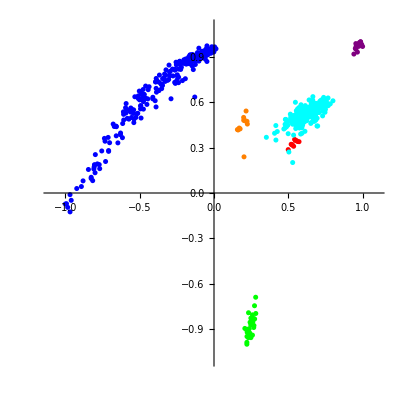
-Graphics- | -Graphics3D-

```mathematica
allDistances=allDists;
allSpecies=allData;
myplotrange2d={{-1.1,1.1},{-1.1,1.1}};
myplotrange3d={{-1.1,1.1},{-1.1,1.1},{-1.1,1.1}};
toIncludeTaxa=Union[Table[allData[[i,2,2]],{i,1,Length@allData}]];
Print[toIncludeTaxa];
organismsInEachTaxa=Table[Sum[fragmentsInEachOrganism[[i1]],{i1,1,i2-1}]+i3,
{i2,1,Length@fragmentsInEachOrganism},{i3,1,fragmentsInEachOrganism[[i2]]}];
Print[Length/@organismsInEachTaxa," in total ",Plus@@(Length/@organismsInEachTaxa)];
filteredDistances=allDists;
(*mds call*)
AbsoluteTiming[mdsres=mds[filteredDistances,3,2];
pts=mdsres[[1]];Print["mds returned coord's for ",Length[pts]," points."]];
(*scaling*)
ptsOld=pts;ptsToBeScaled=Transpose[pts];
ptsX=ptsToBeScaled[[1]];ptsY=ptsToBeScaled[[2]];ptsZ=ptsToBeScaled[[3]];
ptsXScaled=Rescale[ptsX,{Min[ptsX],Max[ptsX]},{-1,1}];
ptsYScaled=Rescale[ptsY,{Min[ptsY],Max[ptsY]},{-1,1}];
ptsZScaled=Rescale[ptsZ,{Min[ptsZ],Max[ptsZ]},{-1,1}];
ptsScaled=Transpose[{ptsXScaled,ptsYScaled,ptsZScaled}];
pts3d=ptsScaled;pts2d={#[[1]],#[[2]]}&/@pts3d;
ptsMST3D=pts3d;ptsMST2D=pts2d;
(*formating data to be ploted*)
graphicsofpts3d={};
copyOfOrganismsInEachTaxa=organismsInEachTaxa;
ptsInFinalPlot3d=Table[{},{i,1,Length[copyOfOrganismsInEachTaxa]}];
ptsInFinalPlot2d=ptsInFinalPlot3d;
For[i1=1,i1≤Plus@@(Length/@organismsInEachTaxa),i1++,minNextInd=Table[Min[copyOfOrganismsInEachTaxa[[i]]],{i,1,Length[copyOfOrganismsInEachTaxa]}];
ind=First[Ordering[minNextInd]];
anotIndex=Min[minNextInd];
(*2d*)AppendTo[ptsInFinalPlot2d[[ind]],Annotation[pts2d[[i1]],{anotIndex,allSpecies[[anotIndex,1]],
allSpecies[[anotIndex,2]],allSpecies[[anotIndex,3]],allSpecies[[anotIndex,4]],
allSpecies[[anotIndex,5]],allSpecies[[anotIndex,6]]},"Mouse"]];
(*3d*)AppendTo[graphicsofpts3d,Annotation[Text["",pts3d[[i1]]],{anotIndex,allSpecies[[anotIndex,1]],allSpecies[[anotIndex,2]],allSpecies[[anotIndex,3]],allSpecies[[anotIndex,4]],allSpecies[[anotIndex,5]],allSpecies[[anotIndex,6]]},"Mouse"]];
AppendTo[ptsInFinalPlot3d[[ind]],pts3d[[i1]]];
(**)copyOfOrganismsInEachTaxa[[ind]]=Drop[copyOfOrganismsInEachTaxa[[ind]],1];];
(*coloring*)
cl=Take[{Blue,Green,Red,Cyan,Purple,Orange,Gray,Brown,Black,Pink,Yellow,Magenta,
RGBColor[50/255,205/255,50/255],Blue,Blue,Blue,Blue,Blue,Blue,Blue,Blue,Blue,Blue,Blue,Blue,Blue},Length@toIncludeTaxa];
colors=cl/.{"Lime":>RGBColor[50/255,205/255,50/255],"AmphibianTurquoise":>RGBColor[0,229/255,238/255],
"DarkGreen":>RGBColor[0,100/255,0],"InsectBrown":>Brown,"Red":>Red,"Blue":>Blue,"ReptileGreen":>Green,
"Yellow":>Yellow,"FungiOrange":>Orange,"BirdOrange":>Orange,"DeepPink":>Pink,"Gray":>Gray,"Purple":>Purple,
"Cyan":>Cyan,"Magenta":>Magenta,"Orange":>Orange,"Green":>Green,"Pink":>Pink,"Brown":>Brown,"Black":>Black,"Purple":>Purple};
(*legends*)
legendNames=Text[Style[#,Italic]]&/@Table[ToString[toIncludeTaxa[[i]]]<>": "<>
ToString[Length[organismsInEachTaxa[[i]]]],{i,1,Length@toIncludeTaxa}];
mylegend=SwatchLegend[Take[colors,Length@legendNames],legendNames];
(*ploting*)
myplotstyle=Table[If[Length[ptsInFinalPlot3d[[i]]]>0,{colors[[i]],ps},{}],{i,1,Length[colors]}];
myplotstyle=Select[myplotstyle,Length[#]>0&];
ptsInFinalPlot3d=Select[ptsInFinalPlot3d,Length[#]>0&];
ptsInFinalPlot2d=Select[ptsInFinalPlot2d,Length[#]>0&];
Print[Grid[{
{ListPlot[ptsInFinalPlot2d,PlotStyle->myplotstyle,PlotRange->myplotrange2d,AspectRatio->1(*,PlotLegends->mylegend*)],
Show[ListPointPlot3D[ptsInFinalPlot3d,PlotStyle->myplotstyle,PlotRange->myplotrange3d,AspectRatio->1,BoxRatios->{1,1,1}(*,PlotLegends->mylegend*)],Graphics3D[graphicsofpts3d]]
}},Frame->All]];
(*info box*)
Print[Dynamic[mousepos=MouseAnnotation[];
info={"ID / Organism","Accession / GenID","Length","Fragment","Header"};
info=Style[#,Black,Bold,Medium]&/@info;
If[mousepos===Null, ,disp={info,{ToString[mousepos[[1]]]<>" / "<>ToString[mousepos[[2,2]]],ToString[mousepos[[3,2]]]<>" / "<>ToString[mousepos[[4,2]]],ToString[mousepos[[5,2]]]<>" bp",mousepos[[7,2]],mousepos[[6,2]]}}];
Grid[Transpose[disp],Alignment->{{Left,Left},{Center,Center}},Background->LightBlue,ItemSize->{{Scaled[.2],Scaled[.8]}},Frame->All]]];
```

```mathematica
(* DISTANCE BETWEEN TWO POINTS *)
allDists[[215,75]]
```

0.744261

### Silhouette Coefficient

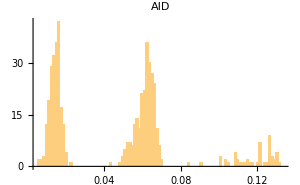
Min | Max | Mean | St.D | Error | Hist of Silh. Coeff
0.00520368 | 0.133545 | 0.0473993 | 0.0328983 | 0 of 508
0.% | -Graphics-

{234,30,10,201,21,12}

Transpose::nmtx: The first two levels of {} cannot be transposed.

{}

Transpose::nmtx: The first two levels of {} cannot be transposed.

({NC_000021.8,NC_000913.3,NC_001136.10,NC_003070.9,NC_004317.2,NC_018092.1}
Transpose[0])

```mathematica
(*** SILHOUETTE ***)
organismsInEachTaxaSilh=organismsInEachTaxa;  (* CHANGE APPROPRIATELY! *)
silh={};
For[i=1,i≤Length[organismsInEachTaxaSilh],i++,
	PrintTemporary["In cluster: "<>ToString@i<>"= "<>ToString[Length@organismsInEachTaxaSilh[[i]]]];
	restClusters=Delete[organismsInEachTaxaSilh,{i}];(*Print[restClusters];*)
	If[Length@organismsInEachTaxaSilh[[i]]>1,
		For[j=1,j≤Length[organismsInEachTaxaSilh[[i]]],j++,
			currPoint=organismsInEachTaxaSilh[[i,j]];(*Print[currPoint];*)
			restPointsInCluster=Delete[organismsInEachTaxaSilh[[i]],{j}];
			alfa=Mean[allDists[[currPoint]][[restPointsInCluster]]];(*Print[alfa];*)
			betas={};
			For[i1=1,i1≤Length[restClusters],i1++,
				currCluster=restClusters[[i1]];
				If[Length@currCluster>0,(* for empty sets *)
				AppendTo[betas,Mean[allDists[[currPoint]][[currCluster]]]];
			]];(*Print[betas];*)
			minbeta=Min[betas];(*Print[minbeta];*)
			sigmaCoef=(minbeta-alfa)/Max[minbeta,alfa];
			AppendTo[silh,{currPoint,sigmaCoef}];
];]];(*Print["silh=",silh];*)res=Transpose[silh][[2]];
Print[Grid[{{"Min","Max","Mean","St.D","Error","Hist of Silh. Coeff"},
{Min[res],Max[res],Mean[res],StandardDeviation[res],
outliers=Length@Select[res,#<0&];tot=Length[res];ToString[outliers]<>" of "<>
ToString[tot]<>"\n"<>ToString[100*N[outliers/tot]]<>"%",
Histogram[res,{Table[Min[res]+i,{i,0,Max[res]-Min[res],(Max[res]-Min[res])/100}]},
PlotLabel->Style[Framed[distTag],16,Black],ImageSize->300]}},Frame->All]];
(* WHICH ARE MISPLACED {Length@silh,Select[silh,#[[2]]<0&]}; *)
(* EXTRA INFO ON SILHOUETTE *)
Print[Length@#&/@organismsInEachTaxaSilh];
(* IDs of them and Names*) 
wrong=Transpose[Select[silh,#[[2]]<0&]][[1]];
Print[Table[ind=Table[Boole[MemberQ[{toIncludeTaxa[[j]]},allSpecies[[wrong[[i]],2,2]]]],
{j,1,Length@toIncludeTaxa}];{wrong[[i]],allSpecies[[wrong[[i]],1,2]],
ImageResize[Graphics[{ind.colors,Rectangle[]}],20]},{i,1,Length@wrong}]//MatrixForm];
(* how many per cluster *)
wrongPerCluster=Count[#,True]&/@ Transpose[Table[MemberQ[{toIncludeTaxa[[j]]},
allSpecies[[wrong[[i]],2,2]]],{i,1,Length@wrong},{j,1,Length@toIncludeTaxa}]];{toIncludeTaxa,wrongPerCluster}//MatrixForm
```

### Cor. with Idealized

```mathematica
finald=allDists;numOfSlidWinds=fragmentsInEachOrganism;Print[numOfSlidWinds];
ranges=Table[∑_(i=1)^j numOfSlidWinds[[i]],{j,1,Length@numOfSlidWinds}];
PrependTo[ranges,0];Print[ranges];
findposition[x_]:=Module[{j},
For[j=1,j≤Length[ranges]-1,j++,
If[ranges[[j]]≤x≤ranges[[j+1]],Break[]]];Return[j]
];PrintTemporary[Dynamic[{i,j}]];
newd=Table[If[findposition[i]==findposition[j],0,1],{i,1,Length[finald]},{j,1,Length[finald]}];
correlationOptimalDistMatr=Correlation[Flatten@finald,Flatten@newd];
Print["correlOptimalDistMatr=",correlationOptimalDistMatr];
```

{234,30,10,201,21,12}

{0,234,264,274,475,496,508}

correlOptimalDistMatr=0.526575

### Hist. Overlap

```mathematica
(****** REPRODUCE HISTOGRAM *****)
finald=allDists;Print[Dimensions[finald]];
dims=fragmentsInEachOrganism;Print[dims];
toget=Table[i22,{i22,1,Length@files}];
Print[toget];
allforhist={};For[j1=1,j1≤Length[toget],j1++,
AppendTo[allforhist,getUpperHalf[Take[finald,{(∑_(k=1)^(toget[[j1]]-1) dims[[k]])+1,(∑_(k=1)^(toget[[j1]]-1) dims[[k]])+dims[[toget[[j1]]]]},
{(∑_(k=1)^(toget[[j1]]-1) dims[[k]])+1,(∑_(k=1)^(toget[[j1]]-1) dims[[k]])+dims[[toget[[j1]]]]}]]]
];Print[Dimensions@#&/@allforhist];
allpairforhist={};For[j2=1,j2≤Length[toget],j2++,For[j3=j2+1,j3≤Length[toget],j3++,
AppendTo[allpairforhist,Take[finald,{(∑_(k=1)^(toget[[j2]]-1) dims[[k]])+1,(∑_(k=1)^(toget[[j2]]-1) dims[[k]])+dims[[toget[[j2]]]]},
{(∑_(k=1)^(toget[[j3]]-1) dims[[k]])+1,(∑_(k=1)^(toget[[j3]]-1) dims[[k]])+dims[[toget[[j3]]]]}]];
]];Print[Dimensions@#&/@allpairforhist];
finalhist={};For[j4=1,j4≤Length[allforhist],j4++,
AppendTo[finalhist,Select[Flatten[allforhist[[j4]]],#>0&]]];
For[j5=1,j5≤Length[allpairforhist],j5++,
AppendTo[finalhist,Select[Flatten[allpairforhist[[j5]]],#>0&]]
];Print[Dimensions@#&/@finalhist];
(* reproduce hist with 100 intervals *)
binrange=Table[i,{i,Min[finalhist],Max[finalhist],(Max[finalhist]-Min[finalhist])/100}];
tmphist=Histogram[finalhist,{binrange},ImageSize->{400}, ChartStyle->colors(* change specific colors*),
PlotLabel->Style[Framed[distTag],16,Black]];(*Print[tmphist];*)
Print[Length@#&/@finalhist];
myf[x1_,x2_,x3_]:=Module[{},
For[ind=1,ind≤Length@finalhist,ind++,
Subscript[vals, ind]=HistogramList[finalhist[[ind]],{binrange}][[2]]
];
iIndex=x1;
jIndex=x2;
ijInd=x3;
(*Print[{Subscript[vals, iIndex],Subscript[vals, jIndex],Subscript[vals, ijInd]}];
Print[Plus@@#&/@{Subscript[vals, iIndex],Subscript[vals, jIndex],Subscript[vals, ijInd]}];*)
(***   ***)
Subscript[diff, 13]=Table[Min[Subscript[vals, iIndex][[i]],Subscript[vals, ijInd][[i]]],{i,1,Length@Subscript[vals, ijInd]}];
Subscript[diff, 23]=Table[Min[Subscript[vals, jIndex][[i]],Subscript[vals, ijInd][[i]]],{i,1,Length@Subscript[vals, ijInd]}];
Subscript[uni, 13]=Table[Max[Subscript[vals, iIndex][[i]],Subscript[vals, ijInd][[i]]],{i,1,Length@Subscript[vals, ijInd]}];
Subscript[uni, 23]=Table[Max[Subscript[vals, jIndex][[i]],Subscript[vals, ijInd][[i]]],{i,1,Length@Subscript[vals, ijInd]}];
step=(Max[finalhist]-Min[finalhist])/100;
h=100*(2*step*Plus@@Subscript[diff, 13])/(step*(Plus@@Subscript[vals, iIndex]+Plus@@Subscript[vals, ijInd]));
a=100*(2*step*Plus@@Subscript[diff, 23])/(step*(Plus@@Subscript[vals, jIndex]+Plus@@Subscript[vals, ijInd]));
(*Print[{h,a,(h+a)/2}];*)
r1=(step*(Plus@@Subscript[diff, 13]))/(step*(Plus@@Subscript[uni, 13]));
r2=(step*(Plus@@Subscript[diff, 23]))/(step*(Plus@@Subscript[uni, 23]));
(*Print[{r1,r2}];*)
tmpdims=Dimensions@#&/@finalhist;
(*Print[{tmpdims[[ijInd,1]]/tmpdims[[iIndex,1]]*r1,tmpdims[[ijInd,1]]/tmpdims[[jIndex,1]]*r2}];
Print["avg=",(tmpdims[[ijInd,1]]/tmpdims[[iIndex,1]]*r1+tmpdims[[ijInd,1]]/tmpdims[[jIndex,1]]*r2)/2, " or ",1-(tmpdims[[ijInd,1]]/tmpdims[[iIndex,1]]*r1+tmpdims[[ijInd,1]]/tmpdims[[jIndex,1]]*r2)/2]*)
Return[1-(tmpdims[[ijInd,1]]/tmpdims[[iIndex,1]]*r1+tmpdims[[ijInd,1]]/tmpdims[[jIndex,1]]*r2)/2]];
PrintTemporary[Dynamic[{i,j}]];
resu=Table[{(*i,j,6 + ∑_(k=2)^i (7-k) + j-i,*)
myf[i,j,Length@fragmentsInEachOrganism + ∑_(k=2)^i (Length@fragmentsInEachOrganism+1-k) + j-i]
},{i,1,Length@fragmentsInEachOrganism},{j,i+1,Length@fragmentsInEachOrganism}];
Print[resu//MatrixForm];Print[Mean@Flatten@resu];
```

{508,508}

{234,30,10,201,21,12}

{1,2,3,4,5,6}

{{27261},{435},{45},{20100},{210},{66}}

{{234,30},{234,10},{234,201},{234,21},{234,12},{30,10},{30,201},{30,21},{30,12},{10,201},{10,21},{10,12},{201,21},{201,12},{21,12}}

{{27261},{435},{45},{20100},{210},{66},{7020},{2340},{47034},{4914},{2808},{300},{6030},{630},{360},{2010},{210},{120},{4221},{2412},{252}}

{27261,435,45,20100,210,66,7020,2340,47034,4914,2808,300,6030,630,360,2010,210,120,4221,2412,252}

({{0.999786},{0.87602},{0.712227},{0.993511},{0.920523}}
{{1.},{0.994625},{1.},{1.}}
{{0.563517},{1.},{1.}}
{{0.99698},{0.99661}}
{{1.}}
{})

0.93692